3.14766×10^8

| Estimate | Standard Error | t-Statistic | P-Value
a | 103.451 | 17.5228 | 5.9038 | 8.47529×10^-7

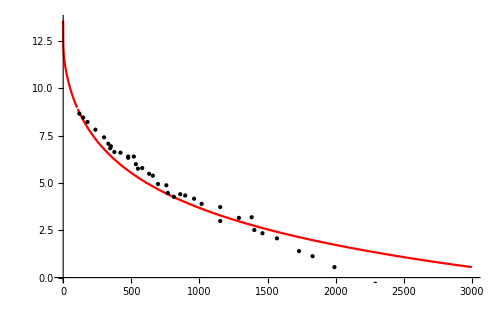

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data_ready_ln_cut.dat"];
L=Length[data];
alpha= 3.1476570491466576*10^8
Ip[R_]:=Piecewise[{{Log[alpha*((2+(R/a)^2)*(Log[(1+Sqrt[1-(R/a)^2])/(R/a)]/(Sqrt[1-(R/a)^2]))-3)/(a^2*(1-(R/a)^2)^2)],R<a},{Log[2*alpha/(7.5*a*a)],R==a},{Log[alpha*((2+(R/a)^2)*(ArcCos[1/(R/a)]/Sqrt[(R/a)^2-1])-3)/(a^2*(1-(R/a)^2)^2)],R>a}}];
(*Plot[Ip[R],{R,0,4}]*)
fit = NonlinearModelFit[data,Ip[R],{a},R,MaxIterations->1000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,0,3000},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```